# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Left Handed Decay width - SM , dim 6 interference )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

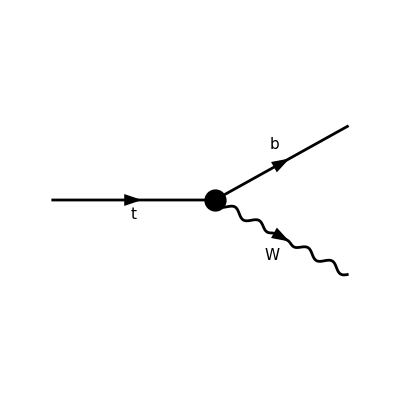

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

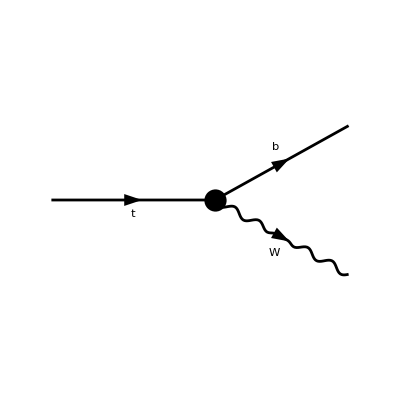

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+

```mathematica
(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+
```

4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-

```mathematica
4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-
```

2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+

```mathematica
2 Sqrt[2] g MinkSP[pt,Eplh] MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2
+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+
```

4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+

```mathematica
4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]*MinkSP[pt,pW]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]*MinkSP[pt,pW]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]*MinkSP[pt,pW]+MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-I ((LeviCivitaContraction[pb,pt,Epclh,Eplh]-I (MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]))*MinkSP[pW,pW]-LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]+LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh])+(MinkSP[pb,pt]*MinkSP[pW,pW]-2 MinkSP[pb,pW]*MinkSP[pt,pW])*MinkSP[Epclh,Eplh]))+
```

(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+

```mathematica
Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^4+
```

128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+

```mathematica
128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+
```

32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-

```mathematica
32 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh]-32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[pb,pW] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D]-
```

ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+

```mathematica
I LeviCivitaContraction[pb,pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[pb,pW,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+
```

4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+

```mathematica
4 C3q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[pb,Eplh]*(MinkSP[pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Epclh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+
```

(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
MinkSP[pb,Epclh]*(MinkSP[pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Eplh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))
```

```mathematica
(* CALCULATION OF M^2 AND OTHERS*)
```

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
Eplh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]-I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]+I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
Epclh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]+I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]-I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt=(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pb,Pw]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epclh,Eplh]+I (MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[Pt,Pw]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epclh,Eplh]+I (MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pw,Pw]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pt,Pw]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g MinkSP[Pt,Eplh] MinkSP[Pw,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pw,Pw]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pt,Pw]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pb,Pw]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]*MinkSP[Pt,Pw]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]*MinkSP[Pt,Pw]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]*MinkSP[Pt,Pw]+MinkSP[Pb,Pw]*MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Pw]*MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pb,Pt]*MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-I ((LeviCivitaContraction[Pb,Pt,Epclh,Eplh]-I (MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]))*MinkSP[Pw,Pw]-LeviCivitaContraction[Pb,Pt,Pw,Eplh]*MinkSP[Pw,Epclh]+LeviCivitaContraction[Pb,Pt,Pw,Epclh]*MinkSP[Pw,Eplh])+(MinkSP[Pb,Pt]*MinkSP[Pw,Pw]-2 MinkSP[Pb,Pw]*MinkSP[Pt,Pw])*MinkSP[Epclh,Eplh]))+Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+32 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh]-32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C2q2H4D]-I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[Pb,Pw,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+4 C3q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[Pb,Eplh]*(MinkSP[Pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epclh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+MinkSP[Pb,Epclh]*(MinkSP[Pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Eplh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8)mt Nc (-16 vev^3 Conjugate[C1qdWH3] (EW-pb) (4 mb vev Conjugate[CKM3x3] (EW+pb) (C1quWH3 vev^2+2 CtW Lambda^2)+√2 g (mb Conjugate[CKM3x3] (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+2 Lambda^2 vev^2 Conjugate[C3phiq]+C3q2H4D vev^4+2 Lambda^4)+Lambda^2 vev^2 Conjugate[CHud] (pb-Eb)+vev^4 Conjugate[CudH4D] (pb-Eb))+8 Lambda^2 vev Conjugate[CbW] (Eb-pb) (pb-EW))+32 vev^6 (Conjugate[C1qdWH3])^2 (Eb-pb) (EW-pb)^2+(Conjugate[CKM3x3])^2 (Eb+pb) (8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (4 Re(C2q2H4D)+2 ⅈ Im(C3q2H4D)))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (Conjugate[C2q2H4D]+C2q2H4D+(Conjugate[C3phiq])^2-Re(C3q2H4D)+C3q2H4D))+32 √2 g Lambda^2 vev^5 (EW+pb) (C1quWH3 Conjugate[C3phiq]+CtW (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D))+16 √2 C1quWH3 g vev^7 (EW+pb) (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+32 √2 g Lambda^4 vev^3 (EW+pb) (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+8 Re(C2q2H4D) (Conjugate[C2q2H4D]+2 ⅈ Im(C3q2H4D))+4 C2q2H4D Conjugate[C2q2H4D]+C3q2H4D^2+(Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D])+32 Lambda^4 vev^2 (g^2 Lambda^2 Conjugate[C3phiq]+4 CtW^2 (EW+pb)^2)+64 √2 CtW g Lambda^6 vev (EW+pb)+16 g^2 Lambda^8)-32 Lambda^2 vev Conjugate[CbW] (EW-pb) (4 mb vev Conjugate[CKM3x3] (EW+pb) (C1quWH3 vev^2+2 CtW Lambda^2)+√2 g (mb Conjugate[CKM3x3] (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+2 Lambda^2 vev^2 Conjugate[C3phiq]+C3q2H4D vev^4+2 Lambda^4)+Lambda^2 vev^2 Conjugate[CHud] (pb-Eb)+vev^4 Conjugate[CudH4D] (pb-Eb)))-8 g Lambda^2 vev^2 Conjugate[CHud] (mb Conjugate[CKM3x3] (2 √2 C1quWH3 vev^3 (EW+pb)+g vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+4 √2 CtW Lambda^2 vev (EW+pb)+2 g Lambda^4)+g vev^4 Conjugate[CudH4D] (pb-Eb))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 √2 C1quWH3 vev^3 (EW+pb)+g vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+4 √2 CtW Lambda^2 vev (EW+pb)+2 g Lambda^4)+128 Lambda^4 vev^2 (Conjugate[CbW])^2 (Eb-pb) (EW-pb)^2+4 g^2 Lambda^4 vev^4 (Conjugate[CHud])^2 (Eb-pb)+4 g^2 vev^8 (Conjugate[CudH4D])^2 (Eb-pb))

```mathematica
(* Total Decay Width*)
```

```mathematica
Msqtot=(1/(32 Lambda^8 MinkSP[Pw,Pw])) Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^4-8 g Lambda^2 Conjugate[CHud] (3 MinkSP[Pw,Pw] (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D] (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) vev^2-24 mb Conjugate[CKM3x3] MinkSP[Pw,Pw] (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 MinkSP[Pw,Pw] (MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))+(Conjugate[CKM3x3])^2 (MinkSP[Pb,Pt] MinkSP[Pw,Pw] (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw] (MinkSP[Pt,Pw] (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

1/(32 Lambda^8 (EW-pb) (EW+pb))Nc (4 g^2 Lambda^4 mt (3 Eb EW^2-(Eb-2 EW) pb^2) (Conjugate[CHud])^2 vev^4-8 g Lambda^2 Conjugate[CHud] (g mt (Eb (pb^2-3 EW^2)-2 EW pb^2) Conjugate[CudH4D] vev^4+3 (EW-pb) (EW+pb) (mb mt Conjugate[CKM3x3] (2 g Lambda^2 Conjugate[C3phiq] vev^2+2 √2 EW (2 CtW Lambda^2+C1quWH3 vev^2) vev+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-2 √2 mt (pb^2+Eb EW) vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]))) vev^2-24 mb (EW-pb) (EW+pb) Conjugate[CKM3x3] (g mt Conjugate[CudH4D] (2 g Lambda^2 Conjugate[C3phiq] vev^2+2 √2 EW (2 CtW Lambda^2+C1quWH3 vev^2) vev+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 EW g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 mt (g^2 (3 Eb EW^2-(Eb-2 EW) pb^2) (Conjugate[CudH4D])^2 vev^8+12 √2 g (EW-pb) (EW+pb) (pb^2+Eb EW) (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] vev^5+8 (EW-pb) (EW+pb) (3 Eb EW^2+(Eb+4 EW) pb^2) (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2)+(Conjugate[CKM3x3])^2 (2 mt (pb^2+Eb EW) (EW (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2+24 √2 (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g+64 EW (EW-pb) (EW+pb) (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)+Eb mt (EW-pb) (EW+pb) ((16 Lambda^8+16 (C2q2H4D+C3q2H4D) vev^4 Lambda^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8) g^2+vev^2 (4 (Conjugate[C2q2H4D])^2 vev^6+(Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 ⅈ Im(C3q2H4D) Re(C2q2H4D) vev^6+16 Lambda^4 (Conjugate[C3phiq])^2 vev^2+8 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D] vev^2-16 Lambda^4 Re(C3q2H4D) vev^2+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) g^2-32 (EW-pb) (EW+pb) (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-EW;
(*pb=-Pw;
Eb=(mb^2-mw^2+mt^2)/(2mt);
pw=-(1/(2 mt)) Sqrt[(mt^2-(mw+mb)^2) (mt^2-(mw-mb)^2)];*)
```

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthLeft=Integrate[Msqt *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar}//FullSimplify
```

1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (Conjugate[CudH4D])^2 vev^8+8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 (Conjugate[C1qdWH3])^2 vev^6+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (Conjugate[CHud])^2 vev^4-16 g mb mt^2 Conjugate[CKM3x3] Conjugate[CudH4D] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2+√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) (2 CtW Lambda^2+C1quWH3 vev^2) vev+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)) vev^4+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[C1qdWH3] (8 Lambda^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW] mt^2+4 mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3] mt-√2 g ((mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D] vev^4+Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CHud] vev^2-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) mt) vev^3+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 (Conjugate[CbW])^2 vev^2+8 g Lambda^2 mt^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2+√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) (2 CtW Lambda^2+C1quWH3 vev^2) vev+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4))) vev^2-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g ((mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D] vev^4+Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CHud] vev^2-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (Conjugate[CKM3x3])^2 (16 g^2 mt^2 Lambda^8+32 √2 CtW g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Lambda^6+16 √2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq]) Lambda^4+32 vev^2 (g^2 Lambda^2 Conjugate[C3phiq] mt^2+CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2) Lambda^4+16 √2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+16 vev^4 (g^2 Lambda^2 ((Conjugate[C3phiq])^2+C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) mt^2+2 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2) Lambda^2+g^2 mt^2 vev^8 (4 C2q2H4D^2+4 Conjugate[C2q2H4D] C2q2H4D+C3q2H4D^2+(Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+8 (Conjugate[C2q2H4D]+2 ⅈ Im(C3q2H4D)) Re(C2q2H4D))+8 vev^6 (g^2 Lambda^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re(C2q2H4D)) mt^2+C1quWH3^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2)+8 √2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))

```mathematica
DecayWidthLeftSM=DecayWidthLeft/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 Nc (Conjugate[CKM3x3])^2 √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) (mb^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)+mt^2-mw^2))/(64 π mt^3)

```mathematica
(*DecayWidthLeft2=Normal[Series[DecayWidthLeft, {Lambda,Infinity,6}]]//Simplify*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthTotal=Integrate[Msqtot *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar}//FullSimplify
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
(*DecayWidthTotal2=Normal[Series[DecayWidthTotal, {Lambda,Infinity,6}]]//Simplify*)
```

```mathematica
(* SM limit *)
```

```mathematica
DecayWidthTotalSM=DecayWidthTotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
FL=DecayWidthLeft/DecayWidthTotal//FullSimplify
```

(4 mt^2 mw^2 (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW]+4 mb mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 mt^2+32 √2 CtW g Lambda^6 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+16 √2 g Lambda^4 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq])+g^2 mt^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (C1quWH3^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D]))+16 √2 g Lambda^2 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (2 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+8 √2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
FLSM=FL/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(mw^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)))/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
Clear[Lambda,e,vev,g,mb,mt, mw,CKM3x3]
```

```mathematica
DecayWidthLeftSM8662=Normal[Series[DecayWidthLeft,{Lambda,∞,4}]]//FullSimplify
```

1/(256 mt^5 π)√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2) (4 g^2 mt^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2+1/Lambda^2 8 g mt vev Conjugate[CKM3x3] (2 √2 mb mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]-g mb mt^2 vev Conjugate[CHud]+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3])+1/Lambda^4 vev^2 (8 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 Conjugate[CbW]^2+g^2 mt^2 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]^2+8 √2 g mb mt^2 (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+8 mt^2 Conjugate[CbW] (-√2 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CHud]-2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-8 g^2 mb mt^3 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (2 CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+√2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 mt^2 vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))))

```mathematica
(*Define parameters and constants based on PHYSICAL REVIEW D 100,056023 (2019)*)
Lambda=1000;e=0.31345;vev=246;g=0.6483;mb=4.78;mt=173.0; mw=80.379;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
(*Check the result by LFullOperatorAll file*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=0;
CtW;
CbW=0;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;dFL=0.013; DecayWidthTotalexp=1.41;dDecayWidthTotalexp=0.17;(*dFL=Sqrt[0.008^2+0.014^2];*)
```

```mathematica
Table[{CtW,DecayWidthTotal},{CtW,-1,1,0.2}]//MatrixForm
```

(-1. | 1.24056
-0.8 | 1.28388
-0.6 | 1.32856
-0.4 | 1.3746
-0.2 | 1.42198
0. | 1.47073
0.2 | 1.52082
0.4 | 1.57227
0.6 | 1.62508
0.8 | 1.67924
1. | 1.73475)

```mathematica
Nc=1;
```

```mathematica
DecayWidthTotal/.CtW^2->0
```

6.07723×10^-44 (3.65683×10^42-8.40043×10^13 (-2.44556×10^29-4.84015×10^28 CtW))

```mathematica
FL
```

(7.73459×10^8 (0.+46923.8 (2.01263×10^29+7.46657×10^28 CtW+1936512000000000000 (0.+3.576×10^9 CtW^2))))/(0.-8.40043×10^13 (-2.44556×10^29-4.84015×10^28 CtW-3.64001×10^27 CtW^2)-5.43791×10^17 (-6.72469×10^24+5.00455×10^22 CtW^2))

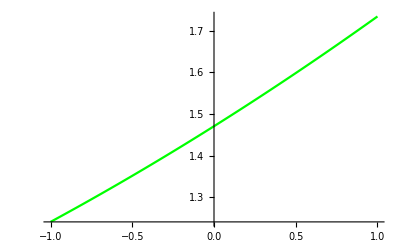

```mathematica
Plot[DecayWidthTotal,{CtW,-1,1},PlotStyle->{Green},PlotRange->All]
```

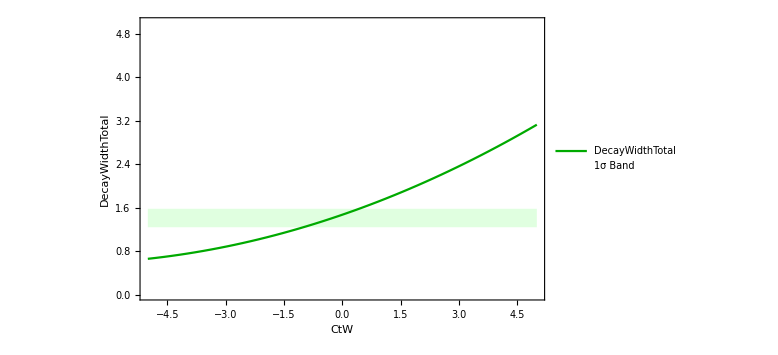

```mathematica
Plot[{DecayWidthTotal,DecayWidthTotalexp-dDecayWidthTotalexp,DecayWidthTotalexp+dDecayWidthTotalexp},{CtW,-5,5},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0,5},AxesLabel->{"CtW","DecayWidthTotal"},PlotLegends->{"DecayWidthTotal","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CtW","DecayWidthTotal"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Lambda=500;
```

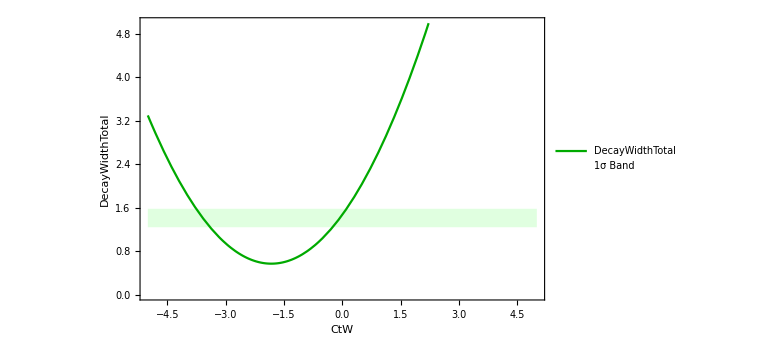

```mathematica
Plot[{DecayWidthTotal,DecayWidthTotalexp-dDecayWidthTotalexp,DecayWidthTotalexp+dDecayWidthTotalexp},{CtW,-5,5},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0,5},AxesLabel->{"CtW","DecayWidthTotal"},PlotLegends->{"DecayWidthTotal","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CtW","DecayWidthTotal"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
N[1/50]
```

0.02

```mathematica
Lambda=500;
```

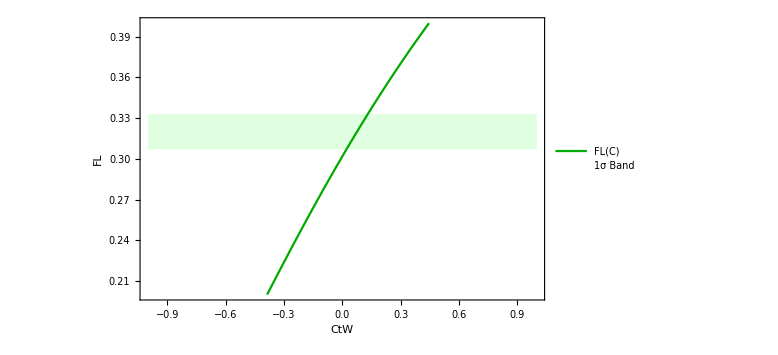

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{CtW,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0.2,0.4},AxesLabel->{"CtW","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CtW","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Lambda=1000;
```

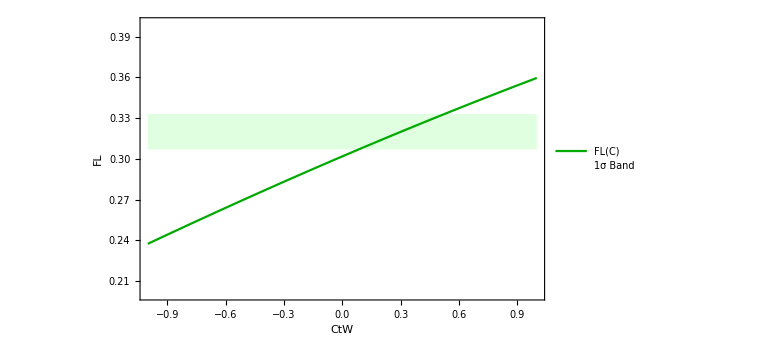

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{CtW,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0.2,0.4},AxesLabel->{"CtW","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CtW","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Clear[CtW]
```

```mathematica
DecayWidthTotalSM
```

1.47073

```mathematica
(* up to Ctw^2*)
```

```mathematica
DecayWidthLeft
```

4.70049×10^-35 (0.+46923.8 (2.01263×10^29+7.46657×10^28 CtW+1936512000000000000 (0.+3.576×10^9 CtW^2)))

```mathematica
DecayWidthLeft1=DecayWidthLeft/.CtW^2->0
```

4.70049×10^-35 (0.+46923.8 (2.01263×10^29+7.46657×10^28 CtW))

```mathematica
CtW=1;
```

```mathematica
DecayWidthLeft2=DecayWidthLeft-DecayWidthLeft1//FullSimplify
```

0.0152741

```mathematica
DecayWidthLeft1-DecayWidthLeftSM//FullSimplify
```

0.164687

```mathematica
DecayWidthTotal
```

6.07723×10^-44 (0.-8.40043×10^13 (-2.44556×10^29-4.84015×10^28 CtW-3.64001×10^27 CtW^2)-5.43791×10^17 (-6.72469×10^24+5.00455×10^22 CtW^2))

```mathematica
(* The result is same*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
Lambda=500;
```

```mathematica
CHud=0;
CtW=0;
CbW=0;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;dFL=0.013; DecayWidthTotalexp=1.41;dDecayWidthTotalexp=0.17;(*dFL=Sqrt[0.008^2+0.014^2];*)
```

```mathematica
Table[{C1quWH3,DecayWidthTotal},{C1quWH3,-1,1,0.2}]//MatrixForm
```

(-1. | 1.35507
-0.8 | 1.37757
-0.6 | 1.40038
-0.4 | 1.42351
-0.2 | 1.44696
0. | 1.47073
0.2 | 1.49481
0.4 | 1.51921
0.6 | 1.54393
0.8 | 1.56897
1. | 1.59432)

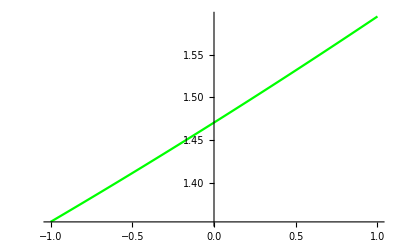

```mathematica
Plot[DecayWidthTotal,{C1quWH3,-1,1},PlotStyle->{Green},PlotRange->All]
```

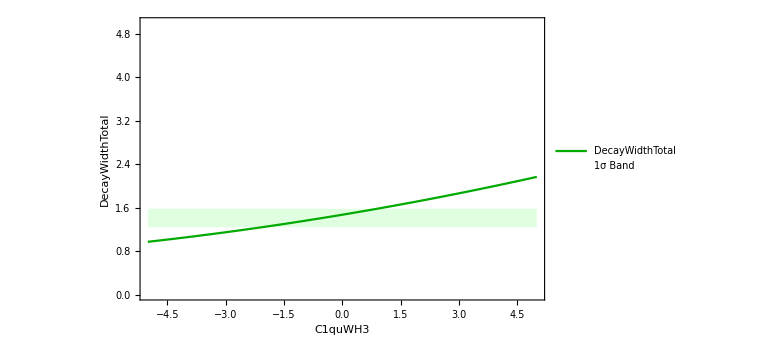

```mathematica
Plot[{DecayWidthTotal,DecayWidthTotalexp-dDecayWidthTotalexp,DecayWidthTotalexp+dDecayWidthTotalexp},{C1quWH3,-5,5},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0,5},AxesLabel->{"C1quWH3","DecayWidthTotal"},PlotLegends->{"DecayWidthTotal","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","DecayWidthTotal"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Lambda=1000;
```

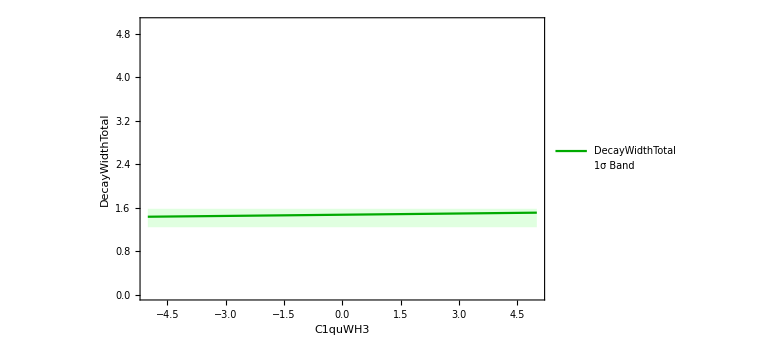

```mathematica
Plot[{DecayWidthTotal,DecayWidthTotalexp-dDecayWidthTotalexp,DecayWidthTotalexp+dDecayWidthTotalexp},{C1quWH3,-5,5},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0,5},AxesLabel->{"C1quWH3","DecayWidthTotal"},PlotLegends->{"DecayWidthTotal","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","DecayWidthTotal"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

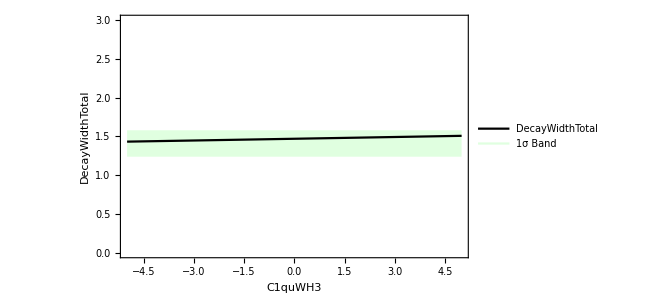

```mathematica
Plot[{DecayWidthTotal,DecayWidthTotalexp - dDecayWidthTotalexp, DecayWidthTotalexp + dDecayWidthTotalexp},  {C1quWH3, -5, 5},Filling -> {2 -> {3}}, FillingStyle -> LightGreen,PlotStyle->{Darker[Black],None,None},  PlotRange -> {0, 3},
    AxesLabel -> {"C1quWH3", "DecayWidthTotal"},  Frame -> True,   FrameLabel -> {"C1quWH3", "DecayWidthTotal"},ImageSize -> Large,
 PlotLegends -> Placed[ LineLegend[  {Darker[Black], LightGreen},   {"DecayWidthTotal", "1σ Band"} ],    Right  ]]
```

```mathematica
(*Export["plot.png", Rasterize[%, ImageSize -> 1000]]*)
```

```mathematica
DecayWidthLeft
```

4.70049×10^-35 (0.+46923.8 (2.01263×10^29+2.25924×10^27 C1quWH3+1772966907744768 (0.+3.576×10^9 C1quWH3^2)))

```mathematica
Decay1=DecayWidthLeft/.C1quWH3^2->0
```

4.70049×10^-35 (0.+46923.8 (2.01263×10^29+2.25924×10^27 C1quWH3))

```mathematica
Decay2=DecayWidthLeft-Decay1//FullSimplify
```

0.+0.0000139841 C1quWH3^2

```mathematica
C1quWH3=1;
```

```mathematica
Decay1
```

0.448899

```mathematica
Decay2
```

0.0000139841

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud;
CtW=0;
CbW=0;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;dFL=0.013; DecayWidthTotalexp=1.41;dDecayWidthTotalexp=0.17;(*dFL=Sqrt[0.008^2+0.014^2];*)
```

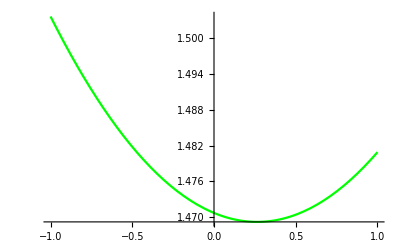

```mathematica
Plot[DecayWidthTotal,{CHud,-1,1},PlotStyle->{Green},PlotRange->All]
```

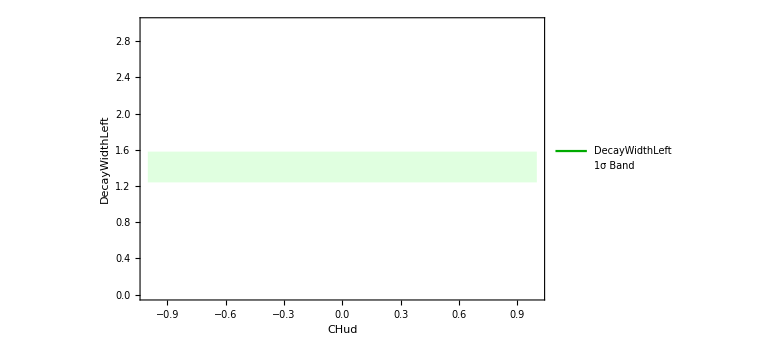

```mathematica
Plot[{DecayWidthTotal,DecayWidthTotalexp-dDecayWidthTotalexp,DecayWidthTotalexp+dDecayWidthTotalexp},{CHud,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{0,3},AxesLabel->{"CHud","DecayWidthLeft"},PlotLegends->{"DecayWidthLeft","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CHud","DecayWidthLeft"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

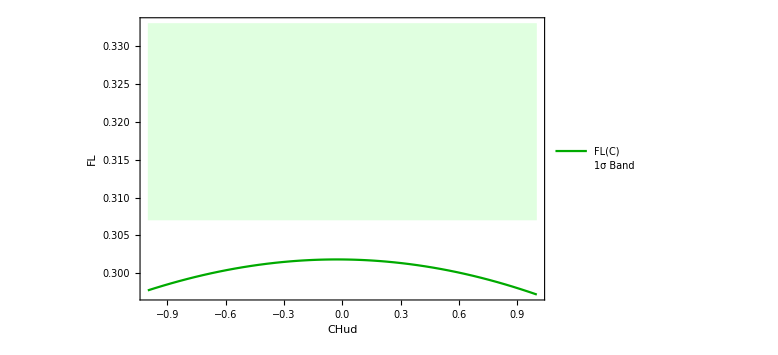

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{CHud,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"CHud","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CHud","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=0;
CtW=0;
CbW;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;dFL=0.013; DecayWidthTotalexp=1.41;dDecayWidthTotalexp=0.15;(*dFL=Sqrt[0.008^2+0.014^2];*)
```

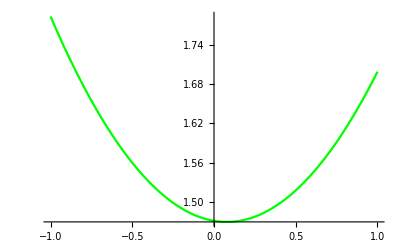

```mathematica
Plot[DecayWidthTotal,{CbW,-1,1},PlotStyle->{Green},PlotRange->All]
```

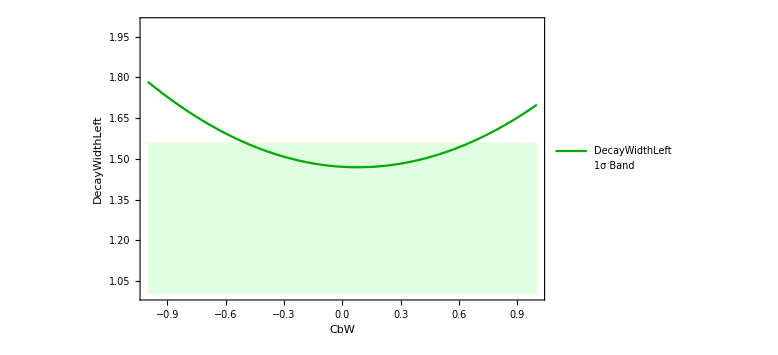

```mathematica
Plot[{DecayWidthTotal,dDecayWidthTotalexp-dDecayWidthTotalexp,DecayWidthTotalexp+dDecayWidthTotalexp},{CbW,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->{1,2},AxesLabel->{"CbW","DecayWidthLeft"},PlotLegends->{"DecayWidthLeft","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CbW","DecayWidthLeft"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

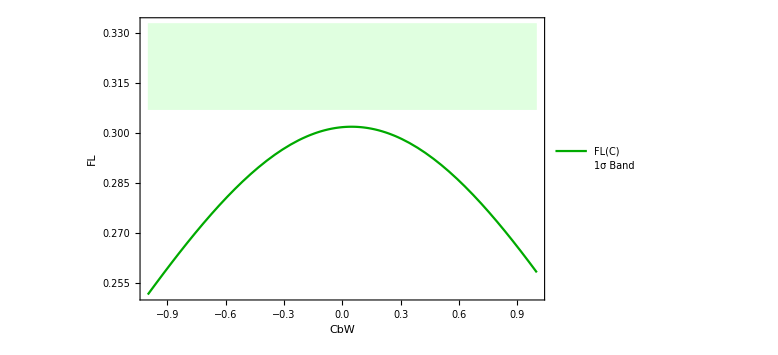

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{CbW,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"CbW","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CbW","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
(* SM Limit *)
```

```mathematica
CHud=0;
CtW=0;
CbW=0;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
Table[{C1quWH3,FL},{C1quWH3,-1,1,0.2}]//MatrixForm
```

(-1. | 0.233139
-0.8 | 0.233478
-0.6 | 0.233817
-0.4 | 0.234157
-0.2 | 0.234496
0. | 0.234835
0.2 | 0.235174
0.4 | 0.235513
0.6 | 0.235851
0.8 | 0.23619
1. | 0.236528)

```mathematica
FL
```

0.301835

```mathematica
FLSM
```

0.301835

```mathematica
FL-FLSM
```

-1.66533×10^-16

```mathematica
C1quWH3
```

0

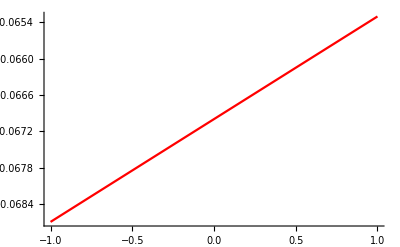

```mathematica
Plot[FL-FLSM,{C1quWH3,-1,1},PlotStyle->{Red},PlotRange->All]
```

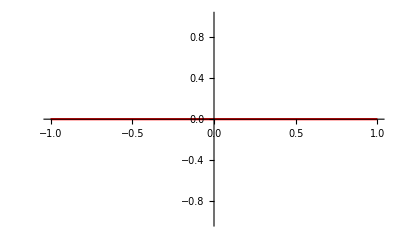

```mathematica
Plot[0,{C1quWH3,-1,1},PlotStyle->{Red},PlotRange->All]
```

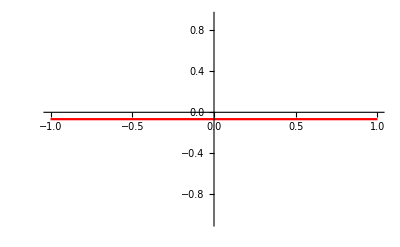

```mathematica
Plot[FL-FLSM,{s,-1,1},PlotStyle->{Red},PlotRange->All]
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

0.234835

```mathematica
FLSM
```

0.301835

```mathematica
FL6=FL-FLSM
```

-0.0669998

```mathematica
Table[{C1quWH3,FL-FLSM},{C1quWH3,-1,1,0.2}]//MatrixForm
```

(-1. | -0.0686959
-0.8 | -0.0683565
-0.6 | -0.0680172
-0.4 | -0.067678
-0.2 | -0.0673389
0. | -0.0669998
0.2 | -0.0666609
0.4 | -0.0663221
0.6 | -0.0659833
0.8 | -0.0656447
1. | -0.0653061)

```mathematica
Plot[FL-FLSM,{C1quWH3,-1,1},PlotStyle->{Red},PlotRange->All]
```

-Graphics-

```mathematica
Plot[FL-FLSM,{s,-1,1},PlotStyle->{Red},PlotRange->All]
```

-Graphics-

```mathematica
Plot[FL6,{C1quWH3,-1,1},PlotStyle->{Red},PlotRange->All]
```

-Graphics-

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq;
C1quWH3;
C1qdWH3;
C2q2H4D;
C3q2H4D;
CudH4D;
```

```mathematica
FL
```

(7.73459×10^8 (1.8518×10^30+1.72899×10^25 Conjugate[C1qdWH3]^2+3.93368×10^25 Conjugate[CudH4D]^2+1.20613×10^17 (1.38398×10^11 Conjugate[CudH4D]-9.56 (2.08041×10^7 (340000.+60516 C1quWH3)+112.156 (2000000000000+3662186256 (C2q2H4D+C3q2H4D))+6.78723×10^6 (2000000 Conjugate[C3phiq]+60516 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-1.5404×10^12 Conjugate[C1qdWH3] (-1.53574×10^15+4.86596×10^10 (340000.+60516 C1quWH3)-158.612 (4.52949×10^13+2.13479×10^11 Conjugate[CudH4D]-1653.88 (2000000000000+121032000000 Conjugate[C3phiq]+3662186256 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1.8231×10^16 (-2.81269×10^8 (340000.+60516 C1quWH3)+0.916835 (4.52949×10^13+2.13479×10^11 Conjugate[CudH4D]-1653.88 (2000000000000+121032000000 Conjugate[C3phiq]+3662186256 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-5.43446×10^15 Conjugate[CudH4D] (2.08041×10^7 (340000.+60516 C1quWH3)+112.156 (2000000000000+3662186256 (C2q2H4D+C3q2H4D))+6.78723×10^6 (2000000 Conjugate[C3phiq]+60516 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+46923.8 (2.13956×10^29+2.25924×10^27 (C1quWH3+0.34 Conjugate[C3phiq])+1936512000000000000 (1.03347×10^8+1.25789×10^10 Conjugate[C3phiq])+1.68704×10^23 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+1772966907744768 (3.576×10^9 C1quWH3^2+1.25789×10^10 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D]))+1.3672×10^26 (C1quWH3 Conjugate[C3phiq]+0.17 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+58594980096000000 (1.21584×10^9 C1quWH3+1.25789×10^10 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+4.13687×10^24 C1quWH3 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(3.65289×10^42+8.67311×10^14 (1.37622×10^27+2.94054×10^23 Conjugate[C1qdWH3]^2-1.56392×10^9 Conjugate[C1qdWH3] (-2.5726×10^16-1.66081×10^14 Conjugate[CudH4D])+1.77691×10^25 Conjugate[CudH4D]+9.35562×10^22 Conjugate[CudH4D]^2)-1.44393×10^22 (-2.26459×10^20-3.31024×10^18 Conjugate[C1qdWH3]-2.38466×10^18 Conjugate[CudH4D]+185295. (1.26519×10^7 (340000.+60516 C1quWH3)+112.156 (2000000000000+3662186256 (C2q2H4D+C3q2H4D))+6.78723×10^6 (2000000 Conjugate[C3phiq]+60516 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+7.55245×10^15 (1.66966×10^9 Conjugate[CudH4D] (-1.26519×10^7 (340000.+60516 C1quWH3)-1.35745×10^13 Conjugate[C3phiq]-112.156 (2000000000000+3662186256 C3q2H4D+3662186256 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-173. (4.14×10^6+60516 Conjugate[C1qdWH3]) (2.19966×10^9 (340000.+60516 C1quWH3)+33342.5 (2000000000000+3662186256 C3q2H4D+121032000000 Conjugate[C3phiq]+3662186256 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8.40043×10^13 (-9.10001×10^14 (340000.+60516 C1quWH3)^2-1.21004×10^10 (340000.+60516 C1quWH3) (2000000000000+3662186256 C3q2H4D+121032000000 Conjugate[C3phiq]+3662186256 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-15284.8 (16000000000000000000000000+13411608173635297536 (4 C2q2H4D^2+C3q2H4D^2)+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+53646432694541190144 Conjugate[C2q2H4D]^2+58594980096000000000000 Conjugate[C3phiq]^2+13411608173635297536 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+484128000000 Conjugate[C3phiq] (4000000000000+7324372512 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+58594980096000000000000 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-5.43791×10^17 (1.25114×10^10 (340000.+60516 C1quWH3)^2-0.420293 (16000000000000000000000000+58594980096000000000000 (C2q2H4D+C3q2H4D)+13411608173635297536 (4 C2q2H4D^2+C3q2H4D^2))-25434.4 (484128 (2000000000000+3662186256 C2q2H4D) Conjugate[C2q2H4D]+886483453872384 Conjugate[C2q2H4D]^2+968256000000000000 Conjugate[C3phiq]^2-443241726936192 C3q2H4D Conjugate[C3q2H4D]+221620863468096 Conjugate[C3q2H4D]^2+3545933815489536 ⅈ Im[C3q2H4D] Re[C2q2H4D]+8000000 Conjugate[C3phiq] (4000000000000+7324372512 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-968256000000000000 Re[C3q2H4D])))

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (1.15737×10^29+4.55774×10^15 (-1.7916×10^14-2.81269×10^8 (85000.+60516 C1quWH3))+46923.8 (9.97023×10^26+1.41202×10^26 (0.+C1quWH3)+14648745024000000 (0.+1.21584×10^9 C1quWH3)+1772966907744768 (0.+3.576×10^9 C1quWH3^2))+3.01532×10^16 (0.-9.56 (1.40195×10^13+2.08041×10^7 (85000.+60516 C1quWH3)))))/(3.02906×10^41-8.40043×10^13 (-9.55298×10^26-1.51255×10^21 (85000.+60516 C1quWH3)-9.10001×10^14 (85000.+60516 C1quWH3)^2)-5.43791×10^17 (-2.62683×10^22+1.25114×10^10 (85000.+60516 C1quWH3)^2)-3.60982×10^21 (-5.66148×10^19+185295. (1.40195×10^13+1.26519×10^7 (85000.+60516 C1quWH3)))+7.55245×10^15 (0.-1.79055×10^8 (4.16781×10^15+2.19966×10^9 (85000.+60516 C1quWH3))))

```mathematica
FLSM
```

0.301835

```mathematica
Table[{C1quWH3,FL},{C1quWH3,-1,1,0.2}]//MatrixForm
```

(-1. | 0.233139
-0.8 | 0.233478
-0.6 | 0.233817
-0.4 | 0.234157
-0.2 | 0.234496
0. | 0.234835
0.2 | 0.235174
0.4 | 0.235513
0.6 | 0.235851
0.8 | 0.23619
1. | 0.236528)

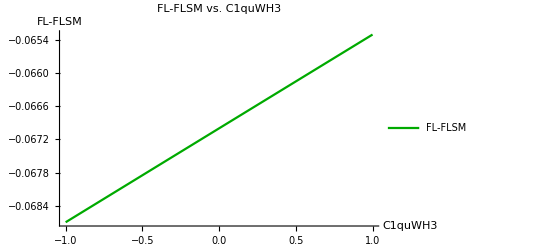

```mathematica
Plot[FL-FLSM,{C1quWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1quWH3 ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

```mathematica
FL-FLSM
```

-0.301835+(7.73459×10^8 (1.8518×10^30+1.8231×10^16 (-2.99114×10^15-2.81269×10^8 (340000.+60516 C1quWH3))+46923.8 (2.14156×10^29+2.25924×10^27 (0.+C1quWH3)+58594980096000000 (0.+1.21584×10^9 C1quWH3)+1772966907744768 (0.+3.576×10^9 C1quWH3^2))+1.20613×10^17 (0.-9.56 (2.24312×10^14+2.08041×10^7 (340000.+60516 C1quWH3)))))/(4.8465×10^42-8.40043×10^13 (-2.44556×10^29-2.42007×10^22 (340000.+60516 C1quWH3)-9.10001×10^14 (340000.+60516 C1quWH3)^2)-5.43791×10^17 (-6.72469×10^24+1.25114×10^10 (340000.+60516 C1quWH3)^2)-1.44393×10^22 (-2.26459×10^20+185295. (2.24312×10^14+1.26519×10^7 (340000.+60516 C1quWH3)))+7.55245×10^15 (0.-7.1622×10^8 (6.66849×10^16+2.19966×10^9 (340000.+60516 C1quWH3))))

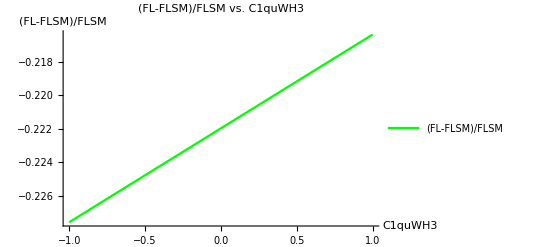

```mathematica
Plot[(FL-FLSM)/FLSM,{C1quWH3,-1,1},PlotStyle->{Green},AxesLabel->{"C1quWH3 ","(FL-FLSM)/FLSM"},PlotLabel->"(FL-FLSM)/FLSM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"(FL-FLSM)/FLSM"}]
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;dFL=0.013;(*dFL=Sqrt[0.008^2+0.014^2];*)
```

```mathematica
FL
```

(7.73459×10^8 (1.8518×10^30+1.8231×10^16 (-2.99114×10^15-2.81269×10^8 (340000.+60516 C1quWH3))+46923.8 (2.14156×10^29+2.25924×10^27 (0.+C1quWH3)+58594980096000000 (0.+1.21584×10^9 C1quWH3)+1772966907744768 (0.+3.576×10^9 C1quWH3^2))+1.20613×10^17 (0.-9.56 (2.24312×10^14+2.08041×10^7 (340000.+60516 C1quWH3)))))/(4.8465×10^42-8.40043×10^13 (-2.44556×10^29-2.42007×10^22 (340000.+60516 C1quWH3)-9.10001×10^14 (340000.+60516 C1quWH3)^2)-5.43791×10^17 (-6.72469×10^24+1.25114×10^10 (340000.+60516 C1quWH3)^2)-1.44393×10^22 (-2.26459×10^20+185295. (2.24312×10^14+1.26519×10^7 (340000.+60516 C1quWH3)))+7.55245×10^15 (0.-7.1622×10^8 (6.66849×10^16+2.19966×10^9 (340000.+60516 C1quWH3))))

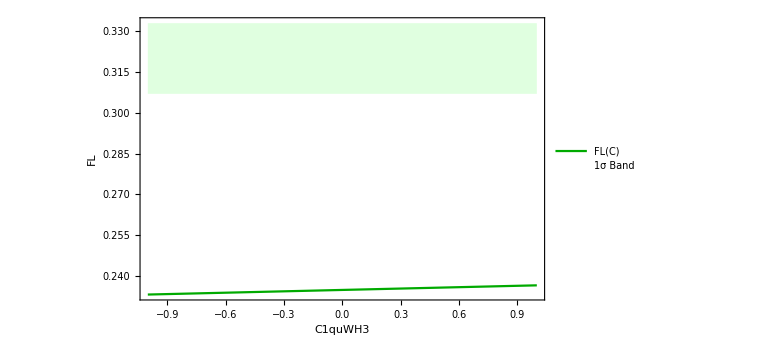

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1quWH3","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

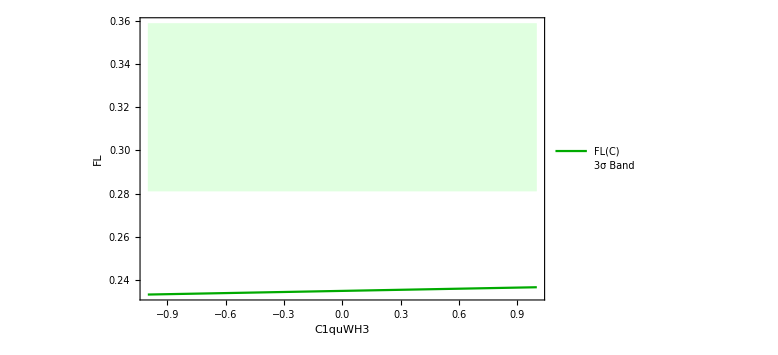

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1quWH3","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Clear[Lambda]
```

```mathematica
Lambda=500;
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

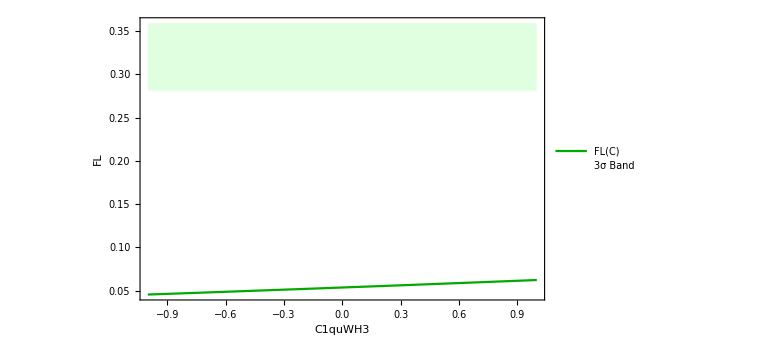

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1quWH3","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
Lambda=1000;
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (9.72782×10^33-8.20226×10^29 Conjugate[C1qdWH3]+1.72899×10^25 Conjugate[C1qdWH3]^2))/(2.85527×10^43-1.44393×10^22 (-1.84098×10^20-3.31024×10^18 Conjugate[C1qdWH3])+8.67311×10^14 (1.37622×10^27+4.02335×10^25 Conjugate[C1qdWH3]+2.94054×10^23 Conjugate[C1qdWH3]^2)+7.55245×10^15 (0.-1.16659×10^19 (4.14×10^6+60516 Conjugate[C1qdWH3])))

```mathematica
FL-FLSM
```

-0.301835+(7.73459×10^8 (9.72782×10^33-8.20226×10^29 Conjugate[C1qdWH3]+1.72899×10^25 Conjugate[C1qdWH3]^2))/(2.85527×10^43-1.44393×10^22 (-1.84098×10^20-3.31024×10^18 Conjugate[C1qdWH3])+8.67311×10^14 (1.37622×10^27+4.02335×10^25 Conjugate[C1qdWH3]+2.94054×10^23 Conjugate[C1qdWH3]^2)+7.55245×10^15 (0.-1.16659×10^19 (4.14×10^6+60516 Conjugate[C1qdWH3])))

```mathematica
Table[{C1qdWH3,FL-FLSM},{C1qdWH3,-1,1,0.2}]//MatrixForm
```

(-1. | -0.0664135
-0.8 | -0.0665307
-0.6 | -0.0666479
-0.4 | -0.0667652
-0.2 | -0.0668825
0. | -0.0669998
0.2 | -0.0671172
0.4 | -0.0672346
0.6 | -0.0673521
0.8 | -0.0674696
1. | -0.0675871)

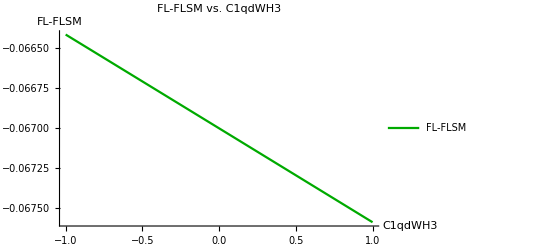

```mathematica
Plot[FL-FLSM,{C1qdWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1qdWH3 ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

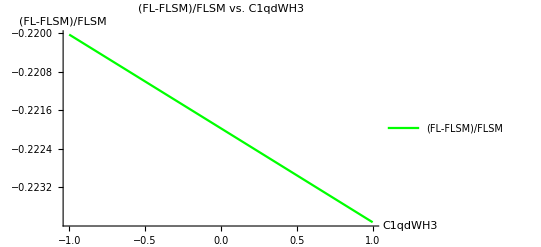

```mathematica
Plot[(FL-FLSM)/FLSM,{C1qdWH3,-1,1},PlotStyle->{Green},AxesLabel->{"C1qdWH3 ","(FL-FLSM)/FLSM"},PlotLabel->"(FL-FLSM)/FLSM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"(FL-FLSM)/FLSM"}]
```

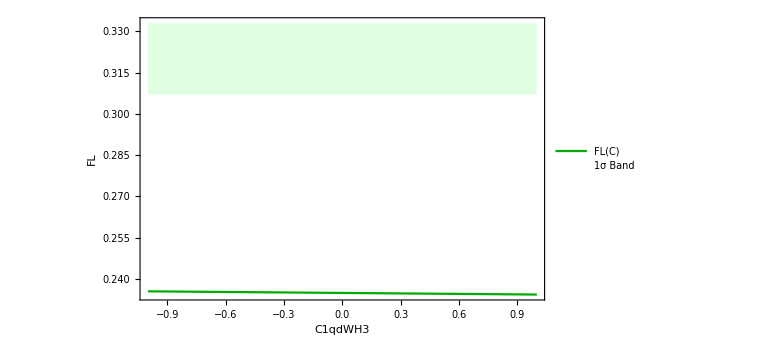

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{C1qdWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1qdWH3","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1qdWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

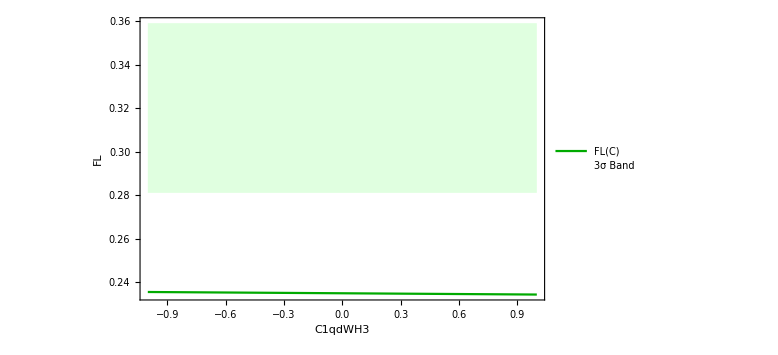

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C1qdWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1qdWH3","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1qdWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (1.8518×10^30+1.20613×10^17 (0.-9.56 (7.0734×10^12+112.156 (2000000000000+3662186256 C2q2H4D)+4.10736×10^11 Conjugate[C2q2H4D]))+1.8231×10^16 (-9.56315×10^13+0.916835 (4.52949×10^13-1653.88 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D]))))+46923.8 (2.14156×10^29+2.32424×10^25 (C2q2H4D+Conjugate[C2q2H4D])+58594980096000000 (0.+1.25789×10^10 (C2q2H4D+Conjugate[C2q2H4D]))+1.68704×10^23 (4 C2q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]+8 Conjugate[C2q2H4D] Re[C2q2H4D]))))/(4.8465×10^42-1.44393×10^22 (-2.26459×10^20+185295. (4.30166×10^12+112.156 (2000000000000+3662186256 C2q2H4D)+4.10736×10^11 Conjugate[C2q2H4D]))-5.43791×10^17 (1.44632×10^21-0.420293 (16000000000000000000000000+58594980096000000000000 C2q2H4D+53646432694541190144 C2q2H4D^2)-25434.4 (484128 (2000000000000+3662186256 C2q2H4D) Conjugate[C2q2H4D]+886483453872384 Conjugate[C2q2H4D]^2))-8.40043×10^13 (-1.05196×10^26-4.11413×10^15 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D]))-15284.8 (16000000000000000000000000+53646432694541190144 C2q2H4D^2+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+53646432694541190144 Conjugate[C2q2H4D]^2+58594980096000000000000 (C2q2H4D+Conjugate[C2q2H4D])))+7.55245×10^15 (0.-7.1622×10^8 (7.47886×10^14+33342.5 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D])))))

```mathematica
Table[{C2q2H4D,FL-FLSM},{C2q2H4D,-1,1,0.2}]//MatrixForm
```

(-1. | -0.0674042+0. ⅈ
-0.8 | -0.0673231+0. ⅈ
-0.6 | -0.0672421+0. ⅈ
-0.4 | -0.0671612+0. ⅈ
-0.2 | -0.0670804+0. ⅈ
0. | -0.0669998+0. ⅈ
0.2 | -0.0669193+0. ⅈ
0.4 | -0.0668389+0. ⅈ
0.6 | -0.0667587+0. ⅈ
0.8 | -0.0666786+0. ⅈ
1. | -0.0665986+0. ⅈ)

```mathematica
FL-FLSM
```

-0.301835+(7.73459×10^8 (1.8518×10^30+1.20613×10^17 (0.-9.56 (7.0734×10^12+112.156 (2000000000000+3662186256 C2q2H4D)+4.10736×10^11 Conjugate[C2q2H4D]))+1.8231×10^16 (-9.56315×10^13+0.916835 (4.52949×10^13-1653.88 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D]))))+46923.8 (2.14156×10^29+2.32424×10^25 (C2q2H4D+Conjugate[C2q2H4D])+58594980096000000 (0.+1.25789×10^10 (C2q2H4D+Conjugate[C2q2H4D]))+1.68704×10^23 (4 C2q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]+8 Conjugate[C2q2H4D] Re[C2q2H4D]))))/(4.8465×10^42-1.44393×10^22 (-2.26459×10^20+185295. (4.30166×10^12+112.156 (2000000000000+3662186256 C2q2H4D)+4.10736×10^11 Conjugate[C2q2H4D]))-5.43791×10^17 (1.44632×10^21-0.420293 (16000000000000000000000000+58594980096000000000000 C2q2H4D+53646432694541190144 C2q2H4D^2)-25434.4 (484128 (2000000000000+3662186256 C2q2H4D) Conjugate[C2q2H4D]+886483453872384 Conjugate[C2q2H4D]^2))-8.40043×10^13 (-1.05196×10^26-4.11413×10^15 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D]))-15284.8 (16000000000000000000000000+53646432694541190144 C2q2H4D^2+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+53646432694541190144 Conjugate[C2q2H4D]^2+58594980096000000000000 (C2q2H4D+Conjugate[C2q2H4D])))+7.55245×10^15 (0.-7.1622×10^8 (7.47886×10^14+33342.5 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D])))))

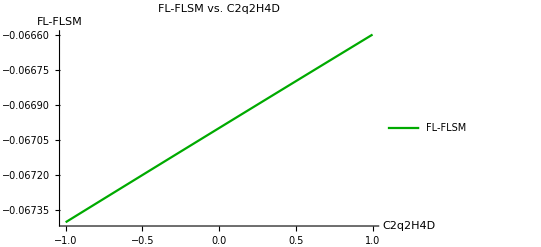

```mathematica
Plot[FL-FLSM,{C2q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C2q2H4D ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

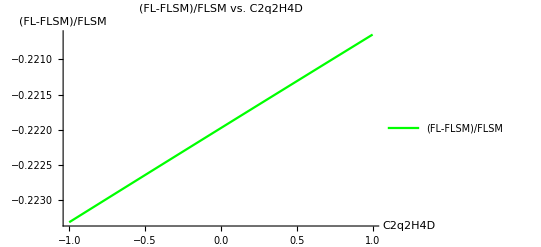

```mathematica
Plot[(FL-FLSM)/FLSM,{C2q2H4D,-1,1},PlotStyle->{Green},AxesLabel->{"C2q2H4D ","(FL-FLSM)/FLSM"},PlotLabel->"(FL-FLSM)/FLSM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"(FL-FLSM)/FLSM"}]
```

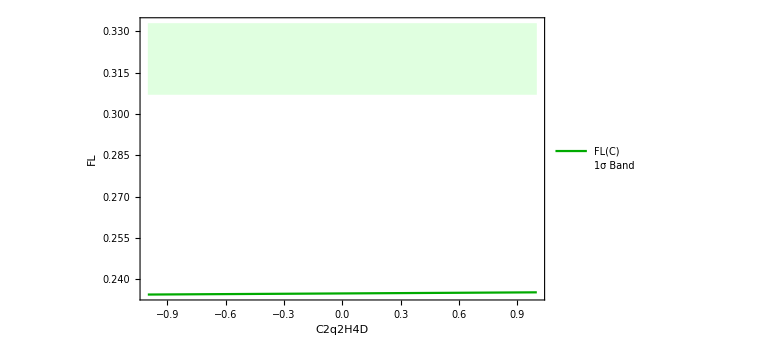

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{C2q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C2q2H4D","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C2q2H4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (1.8518×10^30+1.8231×10^16 (-9.56315×10^13+0.916835 (4.52949×10^13-1653.88 (2000000000000+3662186256 (C3q2H4D-Re[C3q2H4D]))))+1.20613×10^17 (0.-9.56 (7.0734×10^12+112.156 (2000000000000+3662186256 C3q2H4D)-4.10736×10^11 Re[C3q2H4D]))+46923.8 (2.14156×10^29+1.68704×10^23 (C3q2H4D^2-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2)+58594980096000000 (0.+1.25789×10^10 (C3q2H4D-Re[C3q2H4D]))+2.32424×10^25 (C3q2H4D-Re[C3q2H4D]))))/(4.8465×10^42+7.55245×10^15 (0.-7.1622×10^8 (7.47886×10^14+33342.5 (2000000000000+3662186256 C3q2H4D-3662186256 Re[C3q2H4D])))-5.43791×10^17 (1.44632×10^21-0.420293 (16000000000000000000000000+58594980096000000000000 C3q2H4D+13411608173635297536 C3q2H4D^2)-25434.4 (-443241726936192 C3q2H4D Conjugate[C3q2H4D]+221620863468096 Conjugate[C3q2H4D]^2-968256000000000000 Re[C3q2H4D]))-1.44393×10^22 (-2.26459×10^20+185295. (4.30166×10^12+112.156 (2000000000000+3662186256 C3q2H4D)-4.10736×10^11 Re[C3q2H4D]))-8.40043×10^13 (-1.05196×10^26-15284.8 (16000000000000000000000000+13411608173635297536 C3q2H4D^2+13411608173635297536 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2)+58594980096000000000000 (C3q2H4D-Re[C3q2H4D]))-4.11413×10^15 (2000000000000+3662186256 C3q2H4D-3662186256 Re[C3q2H4D])))

```mathematica
Table[{C3q2H4D,FL-FLSM},{C3q2H4D,-1,1,0.2}]
```

{{-1.,-0.0669998},{-0.8,-0.0669998},{-0.6,-0.0669998},{-0.4,-0.0669998},{-0.2,-0.0669998},{0.,-0.0669998},{0.2,-0.0669998},{0.4,-0.0669998},{0.6,-0.0669998},{0.8,-0.0669998},{1.,-0.0669998}}

```mathematica
FL-FLSM
```

-0.301835+(7.73459×10^8 (1.8518×10^30+1.8231×10^16 (-9.56315×10^13+0.916835 (4.52949×10^13-1653.88 (2000000000000+3662186256 (C3q2H4D-Re[C3q2H4D]))))+1.20613×10^17 (0.-9.56 (7.0734×10^12+112.156 (2000000000000+3662186256 C3q2H4D)-4.10736×10^11 Re[C3q2H4D]))+46923.8 (2.14156×10^29+1.68704×10^23 (C3q2H4D^2-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2)+58594980096000000 (0.+1.25789×10^10 (C3q2H4D-Re[C3q2H4D]))+2.32424×10^25 (C3q2H4D-Re[C3q2H4D]))))/(4.8465×10^42+7.55245×10^15 (0.-7.1622×10^8 (7.47886×10^14+33342.5 (2000000000000+3662186256 C3q2H4D-3662186256 Re[C3q2H4D])))-5.43791×10^17 (1.44632×10^21-0.420293 (16000000000000000000000000+58594980096000000000000 C3q2H4D+13411608173635297536 C3q2H4D^2)-25434.4 (-443241726936192 C3q2H4D Conjugate[C3q2H4D]+221620863468096 Conjugate[C3q2H4D]^2-968256000000000000 Re[C3q2H4D]))-1.44393×10^22 (-2.26459×10^20+185295. (4.30166×10^12+112.156 (2000000000000+3662186256 C3q2H4D)-4.10736×10^11 Re[C3q2H4D]))-8.40043×10^13 (-1.05196×10^26-15284.8 (16000000000000000000000000+13411608173635297536 C3q2H4D^2+13411608173635297536 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2)+58594980096000000000000 (C3q2H4D-Re[C3q2H4D]))-4.11413×10^15 (2000000000000+3662186256 C3q2H4D-3662186256 Re[C3q2H4D])))

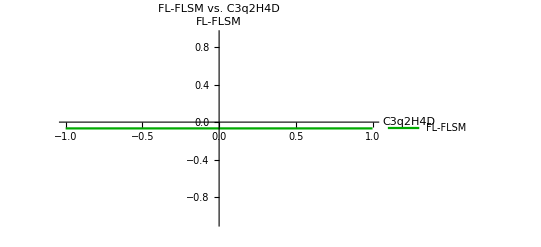

```mathematica
Plot[FL-FLSM,{C3q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C3q2H4D ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

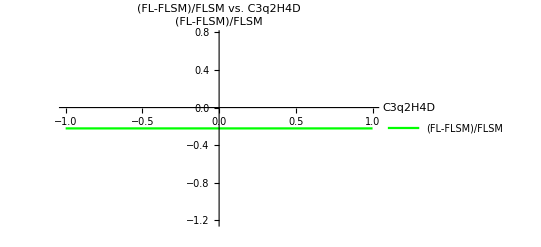

```mathematica
Plot[(FL-FLSM)/FLSM,{C3q2H4D,-1,1},PlotStyle->{Green},AxesLabel->{"C3q2H4D ","(FL-FLSM)/FLSM"},PlotLabel->"(FL-FLSM)/FLSM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"(FL-FLSM)/FLSM"}]
```

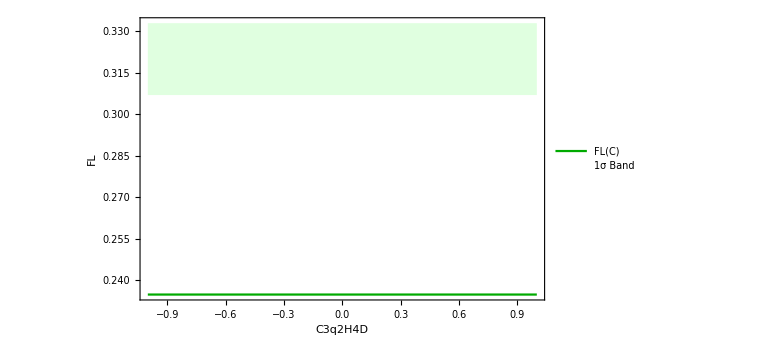

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{C3q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C3q2H4D","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C3q2H4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
Table[{CudH4D,FL-FLSM},{CudH4D,-1,1,0.2}]
```

{{-1.,-0.0666258},{-0.8,-0.0667006},{-0.6,-0.0667754},{-0.4,-0.0668502},{-0.2,-0.066925},{0.,-0.0669998},{0.2,-0.0670746},{0.4,-0.0671495},{0.6,-0.0672243},{0.8,-0.0672991},{1.,-0.0673739}}

```mathematica
FL
```

(7.73459×10^8 (1.00509×10^34-1.25745×10^30 Conjugate[CudH4D]+3.93368×10^25 Conjugate[CudH4D]^2+1.20613×10^17 (-2.21204×10^15+1.38398×10^11 Conjugate[CudH4D])+1.8231×10^16 (-9.56315×10^13+0.916835 (-3.26247×10^15+2.13479×10^11 Conjugate[CudH4D]))))/(2.85527×10^43+7.55245×10^15 (-4.82967×10^25-3.81706×10^23 Conjugate[CudH4D])-1.44393×10^22 (-1.84098×10^20-2.38466×10^18 Conjugate[CudH4D])+8.67311×10^14 (1.37622×10^27+1.77691×10^25 Conjugate[CudH4D]+9.35562×10^22 Conjugate[CudH4D]^2))

```mathematica
FL-FLSM
```

-0.301835+(7.73459×10^8 (1.00509×10^34-1.25745×10^30 Conjugate[CudH4D]+3.93368×10^25 Conjugate[CudH4D]^2+1.20613×10^17 (-2.21204×10^15+1.38398×10^11 Conjugate[CudH4D])+1.8231×10^16 (-9.56315×10^13+0.916835 (-3.26247×10^15+2.13479×10^11 Conjugate[CudH4D]))))/(2.85527×10^43+7.55245×10^15 (-4.82967×10^25-3.81706×10^23 Conjugate[CudH4D])-1.44393×10^22 (-1.84098×10^20-2.38466×10^18 Conjugate[CudH4D])+8.67311×10^14 (1.37622×10^27+1.77691×10^25 Conjugate[CudH4D]+9.35562×10^22 Conjugate[CudH4D]^2))

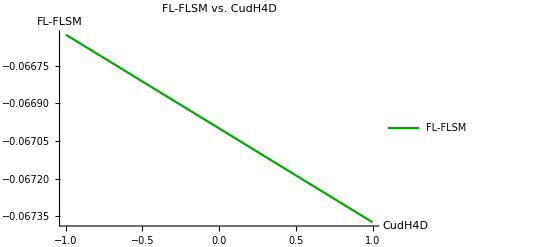

```mathematica
Plot[FL-FLSM,{CudH4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CudH4D ","FL-FLSM"},PlotLabel->"FL-FLSM vs. CudH4D ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

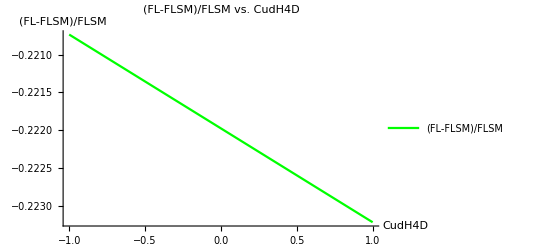

```mathematica
Plot[(FL-FLSM)/FLSM,{CudH4D,-1,1},PlotStyle->{Green},AxesLabel->{"CudH4D ","(FL-FLSM)/FLSM"},PlotLabel->"(FL-FLSM)/FLSM vs. CudH4D ",PlotRange->All,PlotLegends->{"(FL-FLSM)/FLSM"}]
```

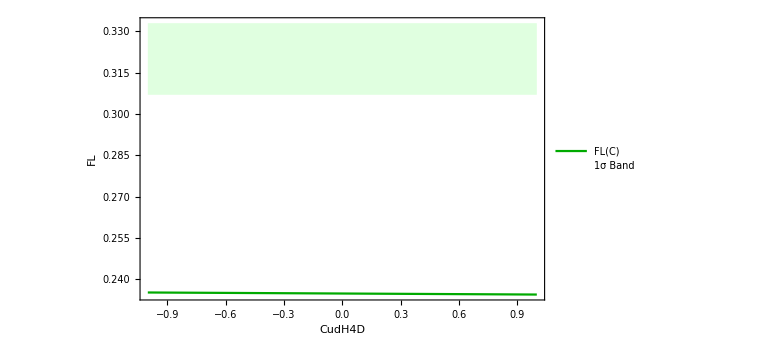

```mathematica
Plot[{FL,FLexp-dFL,FLexp+dFL},{CudH4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"CudH4D","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CudH4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

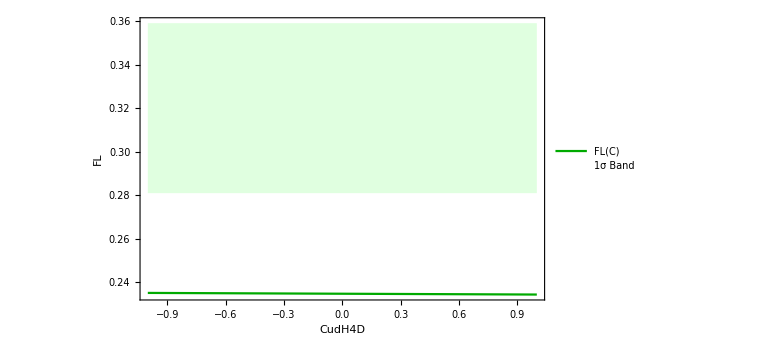

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{CudH4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"CudH4D","FL"},PlotLegends->{"FL(C)","1σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CudH4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (1.89165×10^29-4.1394×10^15 (-3.04609×10^15-2.81269×10^8 (-100000.+60516 C1quWH3))+46923.8 (1.97547×10^29+58594980096000000 (0.-3.576×10^8 C1quWH3)+2.25924×10^27 (0.+C1quWH3)+1772966907744768 (0.+3.576×10^9 C1quWH3^2))-3.89831×10^16 (0.-9.56 (2.24312×10^14+2.08041×10^7 (-100000.+60516 C1quWH3)))))/(4.43129×10^41-8.40043×10^13 (-2.44556×10^29-2.42007×10^22 (-100000.+60516 C1quWH3)-9.10001×10^14 (-100000.+60516 C1quWH3)^2)-5.43791×10^17 (-6.72469×10^24+1.25114×10^10 (-100000.+60516 C1quWH3)^2)+4.6669×10^21 (5.14183×10^19+185295. (2.24312×10^14+1.26519×10^7 (-100000.+60516 C1quWH3)))+7.55245×10^15 (0.+1.6262×10^8 (6.66849×10^16+2.19966×10^9 (-100000.+60516 C1quWH3))))

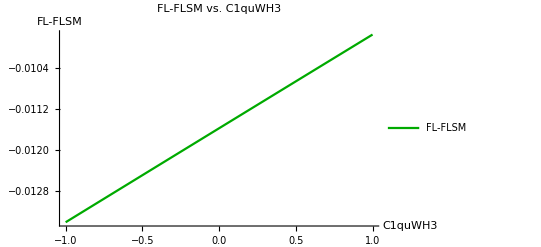

```mathematica
Plot[FL-FLSM,{C1quWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1quWH3 ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

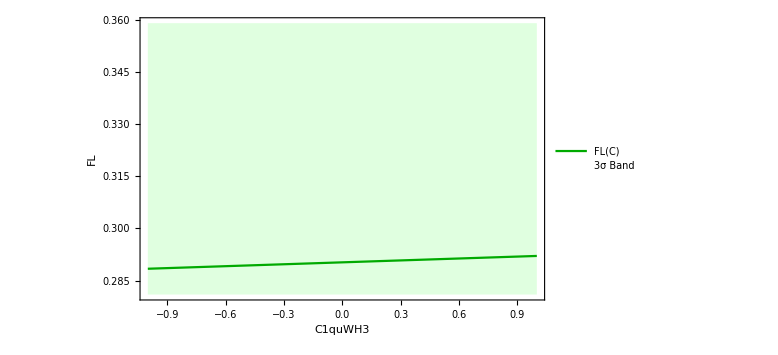

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C1quWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1quWH3","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1quWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (9.36517×10^33-8.04792×10^29 Conjugate[C1qdWH3]+1.72899×10^25 Conjugate[C1qdWH3]^2))/(2.43796×10^43+4.6669×10^21 (9.27478×10^19-3.31024×10^18 Conjugate[C1qdWH3])+8.67311×10^14 (7.09484×10^25-9.13514×10^24 Conjugate[C1qdWH3]+2.94054×10^23 Conjugate[C1qdWH3]^2)+7.55245×10^15 (0.-1.14984×10^19 (-940000.+60516 Conjugate[C1qdWH3])))

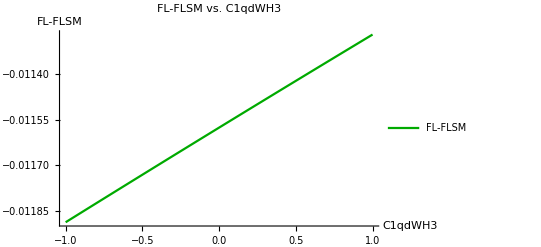

```mathematica
Plot[FL-FLSM,{C1qdWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1qdWH3 ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

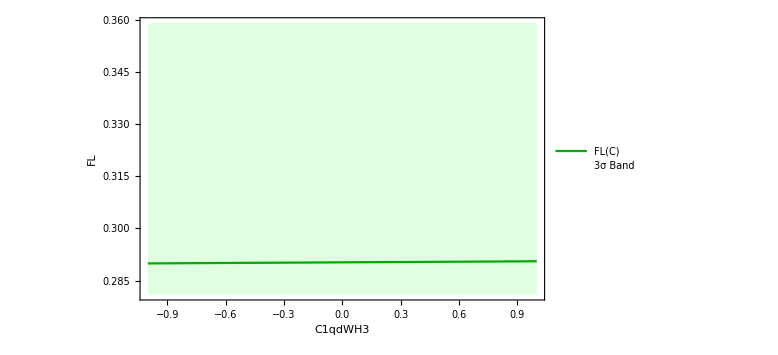

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C1qdWH3,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C1qdWH3","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C1qdWH3","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=-4.15;CtW=-0.05;CbW=-0.47;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (1.89165×10^29-3.89831×10^16 (0.-9.56 (-2.08041×10^12+112.156 (2000000000000+3662186256 C2q2H4D)+4.10736×10^11 Conjugate[C2q2H4D]))-4.1394×10^15 (2.81269×10^13+0.916835 (-1.46397×10^13-1653.88 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D]))))+46923.8 (1.97547×10^29-6.83599×10^24 (C2q2H4D+Conjugate[C2q2H4D])+58594980096000000 (0.+1.25789×10^10 (C2q2H4D+Conjugate[C2q2H4D]))+1.68704×10^23 (4 C2q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]+8 Conjugate[C2q2H4D] Re[C2q2H4D]))))/(4.43129×10^41+4.6669×10^21 (5.14183×10^19+185295. (-1.26519×10^12+112.156 (2000000000000+3662186256 C2q2H4D)+4.10736×10^11 Conjugate[C2q2H4D]))-5.43791×10^17 (1.25114×10^20-0.420293 (16000000000000000000000000+58594980096000000000000 C2q2H4D+53646432694541190144 C2q2H4D^2)-25434.4 (484128 (2000000000000+3662186256 C2q2H4D) Conjugate[C2q2H4D]+886483453872384 Conjugate[C2q2H4D]^2))-8.40043×10^13 (-9.10001×10^24+1.21004×10^15 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D]))-15284.8 (16000000000000000000000000+53646432694541190144 C2q2H4D^2+107292865389082380288 C2q2H4D Conjugate[C2q2H4D]+53646432694541190144 Conjugate[C2q2H4D]^2+58594980096000000000000 (C2q2H4D+Conjugate[C2q2H4D])))+7.55245×10^15 (0.+1.6262×10^8 (-2.19966×10^14+33342.5 (2000000000000+3662186256 (C2q2H4D+Conjugate[C2q2H4D])))))

```mathematica
Table[{C2q2H4D,FL-FLSM},{C2q2H4D,-1,1,0.2}]
```

{{-1.,-0.0116465+0. ⅈ},{-0.8,-0.0116323+0. ⅈ},{-0.6,-0.0116182+0. ⅈ},{-0.4,-0.0116041+0. ⅈ},{-0.2,-0.01159+0. ⅈ},{0.,-0.011576+0. ⅈ},{0.2,-0.011562+0. ⅈ},{0.4,-0.011548+0. ⅈ},{0.6,-0.011534+0. ⅈ},{0.8,-0.0115201+0. ⅈ},{1.,-0.0115062+0. ⅈ}}

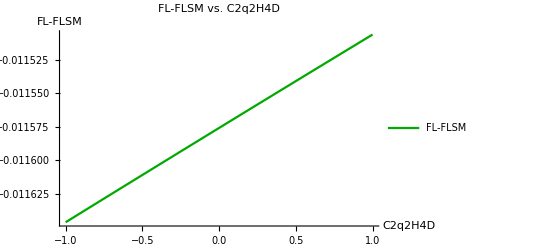

```mathematica
Plot[FL-FLSM,{C2q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C2q2H4D ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

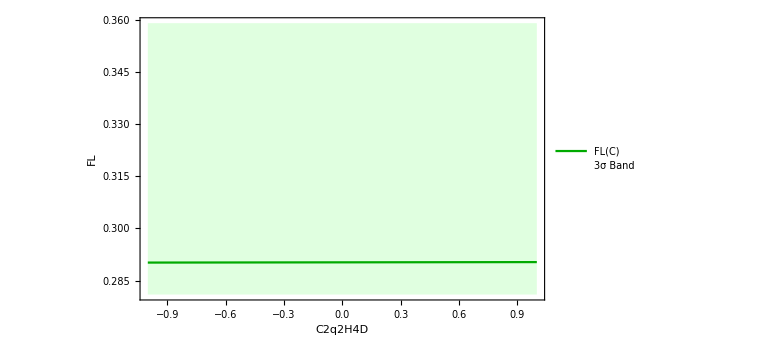

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C2q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C2q2H4D","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C2q2H4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
FL
```

(7.73459×10^8 (1.89165×10^29-4.1394×10^15 (2.81269×10^13+0.916835 (-1.46397×10^13-1653.88 (2000000000000+3662186256 (C3q2H4D-Re[C3q2H4D]))))-3.89831×10^16 (0.-9.56 (-2.08041×10^12+112.156 (2000000000000+3662186256 C3q2H4D)-4.10736×10^11 Re[C3q2H4D]))+46923.8 (1.97547×10^29+1.68704×10^23 (C3q2H4D^2-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2)+58594980096000000 (0.+1.25789×10^10 (C3q2H4D-Re[C3q2H4D]))-6.83599×10^24 (C3q2H4D-Re[C3q2H4D]))))/(4.43129×10^41+7.55245×10^15 (0.+1.6262×10^8 (-2.19966×10^14+33342.5 (2000000000000+3662186256 C3q2H4D-3662186256 Re[C3q2H4D])))-5.43791×10^17 (1.25114×10^20-0.420293 (16000000000000000000000000+58594980096000000000000 C3q2H4D+13411608173635297536 C3q2H4D^2)-25434.4 (-443241726936192 C3q2H4D Conjugate[C3q2H4D]+221620863468096 Conjugate[C3q2H4D]^2-968256000000000000 Re[C3q2H4D]))+4.6669×10^21 (5.14183×10^19+185295. (-1.26519×10^12+112.156 (2000000000000+3662186256 C3q2H4D)-4.10736×10^11 Re[C3q2H4D]))-8.40043×10^13 (-9.10001×10^24-15284.8 (16000000000000000000000000+13411608173635297536 C3q2H4D^2+13411608173635297536 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2)+58594980096000000000000 (C3q2H4D-Re[C3q2H4D]))+1.21004×10^15 (2000000000000+3662186256 C3q2H4D-3662186256 Re[C3q2H4D])))

```mathematica
FLSM
```

0.301835

```mathematica
Table[{C3q2H4D,FL-FLSM},{C3q2H4D,-1,1,0.2}]
```

{{-1.,-0.011576},{-0.8,-0.011576},{-0.6,-0.011576},{-0.4,-0.011576},{-0.2,-0.011576},{0.,-0.011576},{0.2,-0.011576},{0.4,-0.011576},{0.6,-0.011576},{0.8,-0.011576},{1.,-0.011576}}

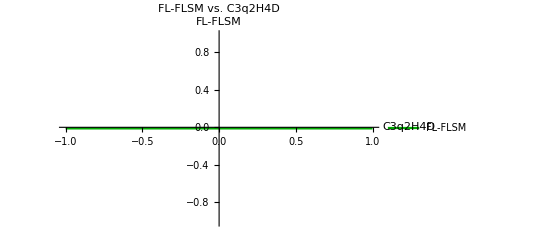

```mathematica
Plot[FL-FLSM,{C3q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C3q2H4D ","FL-FLSM"},PlotLabel->"FL-FLSM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

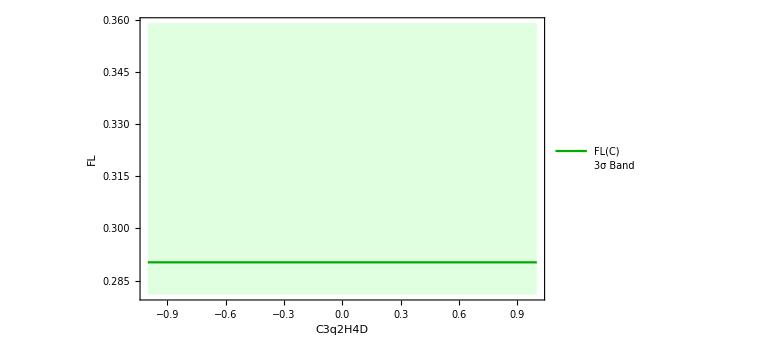

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{C3q2H4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"C3q2H4D","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"C3q2H4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
FL
```

(7.73459×10^8 (9.26986×10^33-1.20771×10^30 Conjugate[CudH4D]+3.93368×10^25 Conjugate[CudH4D]^2-3.89831×10^16 (-2.12453×10^15+1.38398×10^11 Conjugate[CudH4D])-4.1394×10^15 (2.81269×10^13+0.916835 (-3.3224×10^15+2.13479×10^11 Conjugate[CudH4D]))))/(2.43796×10^43+7.55245×10^15 (1.08085×10^25-3.72411×10^23 Conjugate[CudH4D])+4.6669×10^21 (9.27478×10^19-2.38466×10^18 Conjugate[CudH4D])+8.67311×10^14 (7.09484×10^25-4.03454×10^24 Conjugate[CudH4D]+9.35562×10^22 Conjugate[CudH4D]^2))

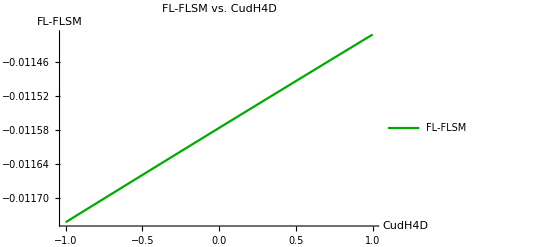

```mathematica
Plot[FL-FLSM,{CudH4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CudH4D ","FL-FLSM"},PlotLabel->"FL-FLSM vs. CudH4D ",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

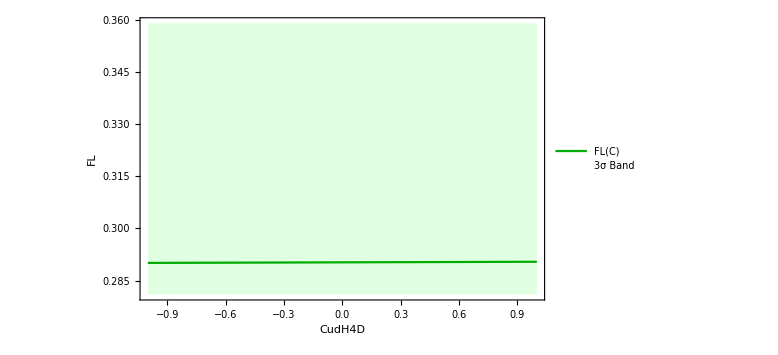

```mathematica
Plot[{FL,FLexp-3*dFL,FLexp+3*dFL},{CudH4D,-1,1},Filling->{2->{3}},FillingStyle->LightGreen,PlotStyle->{Darker[Green],None,None},PlotRange->All,AxesLabel->{"CudH4D","FL"},PlotLegends->{"FL(C)","3σ Band"},ImageSize->Large,Frame->True,FrameLabel->{"CudH4D","FL"},PlotStyle->{{Thick,Darker[Green]},{Dashed},{Dashed}}]
```

```mathematica
(***** Chi squared 2D parameter fit ****)
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=0;
CtW=0;
CbW;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
chi2[CbW_,CudH4D_]:=((FL-FLexp)/dFL)^2
```

```mathematica
grid=Table[{CbW,CudH4D,chi2[CbW,CudH4D]},{CbW,-1,1,0.5},{CudH4D,-1,1,0.5}]//Flatten[#,1]&
```

{{-1.,-1.,3.11854},{-1.,-0.5,3.10674},{-1.,0.,3.0951},{-1.,0.5,3.0836},{-1.,1.,3.07225},{-0.5,-1.,2.30266},{-0.5,-0.5,2.29758},{-0.5,0.,2.29262},{-0.5,0.5,2.28779},{-0.5,1.,2.28307},{0.,-1.,1.95198},{0.,-0.5,1.95221},{0.,0.,1.95255},{0.,0.5,1.953},{0.,1.,1.95356},{0.5,-1.,1.98701},{0.5,-0.5,1.99229},{0.5,0.,1.99768},{0.5,0.5,2.00318},{0.5,1.,2.00881},{1.,-1.,2.41812},{1.,-0.5,2.4294},{1.,0.,2.44083},{1.,0.5,2.45239},{1.,1.,2.46411}}

```mathematica
interpChi2=ListInterpolation[grid,{{-1,1},{-1,1}}];
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

InterpolatingFunction::dmval: Input value {-0.999959,-2.99988} lies outside the range of data in the interpolating function. Extrapolation will be used.

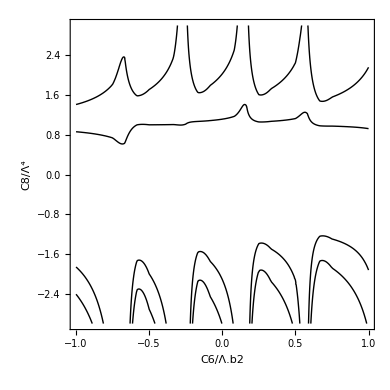

```mathematica
ContourPlot[interpChi2[CbW,CudH4D],{CbW,-1,1},{CudH4D,-3,3},Contours->{2.30,5.99},ContourShading->None,FrameLabel->{"C6/Λ.b2","C8/Λ⁴"},PlotLegends->Automatic,PlotPoints->50]
```

```mathematica
Clear[CbW]
```

```mathematica
(*---تنظیم پارامترها و نقطه بهترین-fit اولیه (برای shift به مرکز)---*)
bestFit={CbW->-0.47,CudH4D->-1.2}; (*فرضی*)

(*تعریف متغیرها برای محور افقی و عمودی*)
{xVar,yVar}={CbW,CudH4D};
{x,y}={xVar,yVar};
```

```mathematica
(*---تابع χ.b2 مدل‌شده---*)
chiSquare[x_,y_,systScale_:1]:=Module[{σbW,σudH4D,ρ,invCov,vec},σbW=3.5*systScale;
σudH4D=5.0*systScale;
ρ=0.4;
invCov=Inverse[{{σbW^2,ρ*σbW*σudH4D},{ρ*σbW*σudH4D,σudH4D^2}}];
vec={x-(CbW/. bestFit),y-(CudH4D/. bestFit)};
vec.invCov.vec];
```

```mathematica
(*---مقدار Δχ.b2 برای 90٪ CL در دو پارامتر---*)
deltaChi2_90=4.605;
```

```mathematica
(*---محدوده رسم---*)
range=10;
```

```mathematica
(*---رسم هر کانتور جداگانه---*)
plotCurrent=ContourPlot[chiSquare[x,y,1]==deltaChi2_90,{x,-range,range},{y,-range,range},ContourStyle->Gray,PlotLegends->None];
```

```mathematica
plotHalfSyst=ContourPlot[chiSquare[x,y,1/2]==deltaChi2_90,{x,-range,range},{y,-range,range},ContourStyle->Blue,PlotLegends->None];
```

```mathematica
plotSqrtNSyst=ContourPlot[chiSquare[x,y,1/Sqrt[100]]==deltaChi2_90,{x,-range,range},{y,-range,range},ContourStyle->Red,PlotLegends->None];
```

```mathematica
(*---ترکیب همه کانتورها با legend---*)
Show[{plotCurrent,plotHalfSyst,plotSqrtNSyst},Frame->True,Axes->False,FrameLabel->{Style[Subscript["C","bW"],14],Style[Subscript["C","udH4D"],14]},PlotRange->All,PlotLegends->Placed[LineLegend[{"Current","HL‑LHC (.bd syst)","HL‑LHC (1/√N syst)"},LineColors->{Gray,Blue,Red}],Bottom],ImageSize->Large]
```

Set::write: Tag Times in 90 deltaChi2_ is Protected.

-Graphics-